```mathematica
SetDirectory[NotebookDirectory[]];
```

Analytic calculations for the cosmic rays + dark matter clumps paper

## Notation

- d: distance to center of clump
- r: distance from center of clump to a point
- θ: angle between line-of-site to center of clump and a point
- m: DM mass

Units check:
	[D_0]=cm^2/s
	[b]=GeV/s
	[λ]=cm^2
	[𝒦]=GeV^2 cm^-6
	[ϕ]=GeV^-1 cm^-2 s^-1 sr^-1

## Setup

```mathematica
bLoss[e_]:=b0(e/E0)^2
DDiff[e_]:=D0(e/E0)^δ
λ[eobs_,esource_]:=(D0 E0)/(b0(1-δ))((E0/eobs)^(1-δ)-(E0/esource)^(1-δ))(*HeavisideTheta[esource-eobs]*)
```

```mathematica
ρnfw[r_]:=ρs (rs/r)^γnfw(1+r/rs)^(γnfw-3)
```

Tidally truncated subhalo profile (from Hooper et al)

```mathematica
ρtt[r_]:=ρ0 (Rb/r)^γtt E^(-r/Rb)
```

```mathematica
$Assumptions={r>0,rs>0,ρs>0,ρ0>0,Rb>0,3/2>γtt>0,3/2>γnfw>0};
```

```mathematica
pySubs={ρs->rhos,ρ0->rho0,γtt->gamma,γnfw->gamma,Pi->pi,Sqrt[x_]:>sqrt[x],cθ->cos[th]};
```

```mathematica
pyFormat[expr_]:=expr/.pySubs/.pySubs//FortranForm
```

## Analysis functions

Profile-dependent factor in clump luminosity

```mathematica
Lclump[ρ_]:=Simplify[Integrate[4π r^2 ρ[r]^2,{r,0,∞}]]
```

Computes 𝒦(θ,r,d)=∫ ⅆ(c_θ [ρ(√(d^2+r^2-2d r c_θ))])^2. This is important because:
	J=(2π)/ΔΩ (∫_0)^∞ⅆr [𝒦(0,r,d) - 𝒦(θ_max,r,d)]
	(d^2 ϕ_(e-))/(dE dr)=c/(4π)(π ⟨σv⟩)/(m^2 (b(E) [4π λ(E,m)])^(3/2)) r^2 exp(-r^2/(4λ(E)))[𝒦(0,r,d) - 𝒦(π,r,d)]

```mathematica
𝒦[ρ_,assumptions_:{}]:=Integrate[ρ[√(d^2+r^2-2d r cθ)]^2,cθ,Assumptions->assumptions]
```

## Results for profiles

### NFW

```mathematica
Lnfw=Lclump[ρnfw]//FullSimplify;
```

```mathematica
𝒦nfw=𝒦[ρnfw]//FullSimplify;
```

```mathematica
𝒦nfwγ1=𝒦[ρnfw[#]/.γnfw->1&]//FullSimplify;
```

```mathematica
pyFormat[Lnfw]>>"mathematica_to_python/L_clump_nfw.py"
pyFormat[𝒦nfw]>>"mathematica_to_python/K_nfw.py"
pyFormat[𝒦nfwγ1]>>"mathematica_to_python/K_nfw_gamma_1.py"
```

### TT

```mathematica
Ltt=Lclump[ρtt]//FullSimplify;
```

π 2^(2 γtt-1) ρ0^2 Rb^3 3-2 γtt

```mathematica
𝒦tt=𝒦[ρtt]//FullSimplify;
```

```mathematica
𝒦ttγ1=𝒦[ρtt,{γtt==1}]//FullSimplify;
```

```mathematica
𝒦ttγgtr1=𝒦[ρtt,{γtt>1}]//FullSimplify;
```

```mathematica
pyFormat[Ltt]>>"mathematica_to_python/L_clump_tt.py"
pyFormat[𝒦tt]>>"mathematica_to_python/K_tt.py"
pyFormat[𝒦ttγ1]>>"mathematica_to_python/K_nfw_gamma_1.py"
pyFormat[𝒦ttγgtr1]>>"mathematica_to_python/K_nfw_gamma_gtr_1.py"
```

#### Scratch

```mathematica
𝒦ttγgtr1/𝒦ttγ1//FullSimplify
```

-(4^(γtt-1) 2-2 γtt(2 √(d^2-2 cθ r d+r^2))/Rb)/(-(2 √(d^2-2 cθ r d+r^2))/Rb)

```mathematica
?ExpIntegralEi
```

ExpIntegralEi[z] gives the exponential integral function Ei(z).

```mathematica
?Gamma
```

Gamma[z] is the Euler gamma function Γ(z). 
Gamma[a,z] is the incomplete gamma function Γ(a,z). 
Gamma[a,z_0,z_1] is the generalized incomplete gamma function Γ(a,z_0)-Γ(a,z_1).

```mathematica
GammaNegA[a_,z_]:=If[
a<0,
1/a(GammaNegA[a+1,z]-z^a E^-z),
Gamma[a,z]
]
```

```mathematica
Gamma[0,1]//N
```

0.219384

```mathematica
With[{x=1.5},
{Gamma[0,x],-ExpIntegralEi[-x]}
]
```

{0.10002,0.10002}

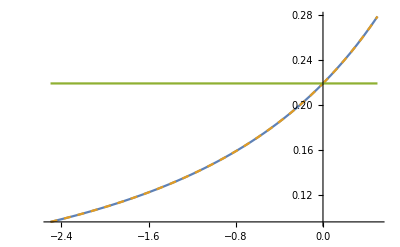

```mathematica
Plot[{Re[Gamma[a,1]],GammaNegA[a,1],Gamma[0,1]//N},{a,-2.5,0.5},PlotStyle->{Normal,Dashed}]
```

## Distribution over γ_TT

Hooper et al claim that the distribution of γ_TT is independent of the subhalo mass:

```mathematica
prγttSubs={γtt50->0.74,σ->0.42,κ->0.10};
```

```mathematica
prγtt[γ_]:=1/(√(2π))1/(σ-κ(γ-γtt50))Exp[-Log[1-(κ(γ-γtt50))/σ]^2/(2 κ^2)]HeavisideTheta[σ/κ+γtt50-γ]HeavisideTheta[γ]
```

Get quartiles

```mathematica
γtt25=NSolve[N[Integrate[prγtt[γ]/.prγttSubs,{γ,0,γ25},Assumptions->{0<γ25<3/2}]]==0.25,γ25]⟦1⟧⟦1⟧⟦2⟧
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

0.516816

```mathematica
γtt75=NSolve[N[Integrate[prγtt[γ]/.prγttSubs,{γ,0,γ75},Assumptions->{0<γ75<3/2}]]==0.75,γ75]⟦1⟧⟦1⟧⟦2⟧
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

1.08222

```mathematica
{γtt25,γtt50,γtt75}/.prγttSubs
```

{0.516816,0.74,1.08222}

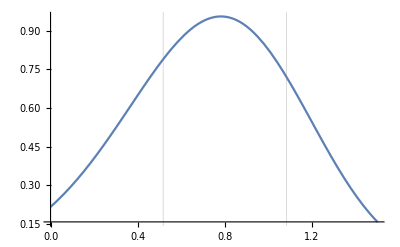

```mathematica
Plot[prγtt[γ]/.prγttSubs,{γ,0,3/2},
GridLines->{{γtt25,γtt75},{}}]
```

## Find velocity distribution within the clump

Eddington’s formula relates the phase space distribution function f(ℰ,L) to ρ(r), with f(ℰ,L)=f(ℰ) (where the equality assumes the velocity distribution is isotropic and L is the angular momentum):

	ℰ=ψ-1/2 v^2>0,
	ψ(r)=(∫_r)^r_0 ⅆr' (G m(r'))/(r')^2
	ρ(r)=∫ⅆ^3 v f(ℰ,L)=4π √2(∫_0)^(ψ(r))ⅆℰ f(ℰ)√(ψ(r)-ℰ)
	f_(v⃗)(v⃗,r)=(f(ℰ,L))/(ρ(r))
	f_v(v,r)=v^2∫ ⅆ Ω_v f_(v⃗)(v⃗,r)
	
	f(ℰ)=1/(√8 π^2)d/dℰ(∫_0)^ℰ ⅆψ/(√(ℰ-ψ))dρ/dψ
            =1/(√8 π^2)(1/(√ℰ)dρ/dψ|_(ψ=0)+(∫_0)^ℰ ⅆψ/(√(ℰ-ψ))(d^2 ρ)/dψ^2)

ⅆℰ=-v ⅆv, ℰ=ψ(r)=ψ(r)-1/2 v^2⇒v=0, ℰ=0=ψ(r)-1/2 v^2⇒v=√(2ψ(r))
ρ(r)=-4π √2(∫_0)^(ψ(r))ⅆv  v f(ψ(r)-1/2 v^2)√(ψ(r)-(ψ(r)-1/2 v^2))
          =4π∫_0^(√(2ψ(r))) ⅆv  v^2 f(ψ(r)-1/2 v^2)

#### Set up necessary potentials and derivatives

```mathematica
GeV to kg=1.78 10^-27;
kpc to m=3.086 10^19;
GSub={G->6.674 10^-11}; (* N m^2/kg^2 *)
c=299792458; (* m/s *)
```

Compute “potential” and derivatives of it and the density

```mathematica
getψρDerivs[ρ_,extraAssumps_:{}]:=Module[{dρ dr,d2ρ dr2,m,ψ,dψ dr,d2ψ dr2},
m[r_]=Simplify[Integrate[4π rp^2 ρ[rp],{rp,0,r},
Assumptions->Join[{r>0},extraAssumps]]];

ψ[r_]=Simplify[Integrate[(G m[rp])/rp^2,{rp,r,∞},Assumptions->Join[{r>0},extraAssumps]]];
dψ dr[r_]=-(G m[r])/r^2;
d2ψ dr2[r_]=(2G m[r])/r^3-4π G ρ[r]//Simplify;

dρ dr[r_]=D[ρ[r],r]//Simplify;
d2ρ dr2[r_]=D[ρ[r],{r,2}]//Simplify;

{m,dρ dr,d2ρ dr2,ψ,dψ dr,d2ψ dr2}
]
```

```mathematica
getψρND[m_,ρ_,dρ dr_,d2ρ dr2_,ψ_,dψ dr_,d2ψ dr2_,rRef_]:=Module[{MRef,ρRef,ψRef,ρND,dρ drND,d2ρ dr2ND,ψND,dψ drND,d2ψ dr2ND},
(* Mass contained within reference radius *)
MRef=m[rRef];

ρRef=MRef/(4/3π rRef^3);
ψRef=(G MRef)/rRef;

ρND[x_]=ρ[r]/ρRef/.{r->x rs}//FullSimplify;
dρ drND[x_]=(dρ dr[r])/ρRef/.{r->x rs}//FullSimplify;
d2ρ dr2ND[x_]=(d2ρ dr2[r])/ρRef/.{r->x rs}//FullSimplify;
ψND[x_]=ψ[r]/ψRef/.{r->x rs}//FullSimplify;
dψ drND[x_]=(dψ dr[r])/ψRef/.{r->x rs}//FullSimplify;
d2ψ dr2ND[x_]=(d2ψ dr2[r])/ψRef/.{r->x rs}//FullSimplify;

{MRef,ρND,dρ drND,d2ρ dr2ND,ψND,dψ drND,d2ψ dr2ND}
]
```

```mathematica
{mnfw,dρ drnfw,d2ρ dr2nfw,ψnfw,dψ drnfw,d2ψ dr2nfw}=getψρDerivs[ρnfw];
```

```mathematica
{MRefnfw,ρNDnfw,dρ drNDnfw,d2ρ dr2NDnfw,ψNDnfw,dψ drNDnfw,d2ψ dr2NDnfw}=getψρND[mnfw,ρnfw,dρ drnfw,d2ρ dr2nfw,ψnfw,dψ drnfw,d2ψ dr2nfw,rs]
```

#### Non-dimensional Eddington inversion

I don’t understand why this is not properly normalized.

```mathematica
fvND[v_,r_,rRef_,MRef_,ρND_,dρ drND_,d2ρ dr2ND_,ψND_,dψ drND_,d2ψ dr2ND_,params_]:=Module[{vRef,fact,integrand,int,vND,xBound},
(* Convert to SI units *)
vRef=√((G MRef GeV to kg(10^2 kpc to m)^3)/(rRef kpc to m));
vND=v/vRef;

(* Normalization and dimensionful factors *)
fact=(√2)/π 1/vRef vND^2/ρND[r];

(* Determine integration bound *)
xBound=xp/.FindRoot[Re[ψND[r/rRef]-1/2 vND^2-ψND[xp]/.params/.GSub]==0,{xp,r/rRef/.params}];

(* Perform the integration *)
integrand[xp_]=1/(√(ψND[r/rRef]-1/2 vND^2-ψND[xp]))1/(dψ drND[xp])(d2ρ dr2ND[xp]-1/(dψ drND[xp])d2ψ dr2ND[xp]dρ drND[xp])//Simplify;

int=NIntegrate[Re[integrand[xp]/.params/.GSub],{xp,∞,xBound}];

(* Debug messages *)
(*Print[xBound,"     ",Re[1/(√(ψND[r/rRef]-1/2 vND^2-ψND[xBound*5]))/.params/.GSub]];
Print[""];*)

(* Combine everything *)
fact*int/.params/.GSub
]
```

### NFW

#### The speed distribution

Choose clump parameters

```mathematica
paramSubs={ρs->129.,rs->0.03,γnfw->0.5}; (* benchmark clump *)
d=0.1;
```

```mathematica
paramSubs={ρs->0.184,rs->24.42,γnfw->0.9999}; (* Milky Way *)
d=24.42*0.3;(*20.;*)
```

Find DM escape velocity at chosen distance

```mathematica
vRef=Re[√((G MRefnfw GeV to kg(10^2 kpc to m)^3)/(rs kpc to m))/.paramSubs/.GSub];
vNDMin=0;
vNDMax=Re[vND/.FindRoot[ψNDnfw[d/rs]-1/2 vND^2==0/.paramSubs/.GSub,{vND,1.}]];
```

Compute f_v(v,r) over a grid

```mathematica
fvNDs=Table[
{v,Re[fvND[v,d,rs,MRefnfw,ρNDnfw,dρ drNDnfw,d2ρ dr2NDnfw,ψNDnfw,dψ drNDnfw,d2ψ dr2NDnfw,paramSubs]]},
{v,vRef vNDMin,vRef vNDMax,(vRef(vNDMax-vNDMin))/100}
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xp near {xp} = {6.50867×10^8}. NIntegrate obtained 4.97036×10^-25 and 1.14774×10^-28 for the integral and error estimates.

Sometimes the integration fails for the last point. Dropping it is the easiest solution:

```mathematica
fvNDs=Drop[fvNDs,-1];
```

Construct an interpolator for the PDF

```mathematica
fvNDsNorm=Re[Integrate[Interpolation[fvNDs][v],{v,vRef vNDMin,vRef vNDMax}]];
fvNDInterp=Interpolation[Transpose[{fvNDs⟦;;,1⟧,fvNDs⟦;;,2⟧/fvNDsNorm}]];
```

InterpolatingFunction::dmvali: The integration endpoint 522335. in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

Find Maxwell-Boltzmann distribution with the same mode

```mathematica
σMB=(Re[MaximalBy[fvNDs,Last]]⟦1⟧⟦1⟧)/(√2);
```

Milky Way case. Compare with known result from Fig. 2 of arxiv:1805.02403 for d=20 kpc: it’s close. Also is close to Fig. 1 of arxiv:1804.05052 for d=0.3×24.42 kpc.

```mathematica
{mwVels,mwfvs}=Transpose[Import["data/eddington_inversion_mw_nfw.csv"]];
```

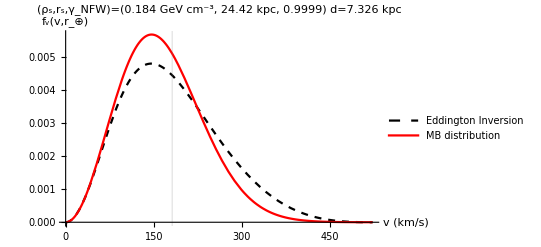

```mathematica
Show[
(*ListPlot[Transpose[{mwVels,mwfvs}]],*)
Plot[
{10^3 fvNDInterp[10^3 v],10^3 PDF[MaxwellDistribution[σMB],10^3 v]},
{v,10^-3 vRef vNDMin,10^-3 vRef vNDMax},
PlotStyle->{{Black,Dashed},Red},
PlotLegends->{"Eddington Inversion","MB distribution"},
AxesLabel->{Style["v (km/s)",16], Style["f_v(v,r_⊕)",14]},
PlotLabel->Style["(ρ_s,r_s,γ_NFW)=("<>ToString[ρs/.paramSubs]<>" GeV cm^-3, "<>ToString[rs/.paramSubs]<>" kpc, "<>ToString[γnfw/.paramSubs]<>")\nd="<>ToString[d]<>" kpc",13],
PlotRange->Full,
GridLines->{{NIntegrate[10^-3 v fvNDInterp[v],{v,0,vRef vNDMax}]},{}}
]
]
```

Compare PDF from Eddington formula with the MB distribution

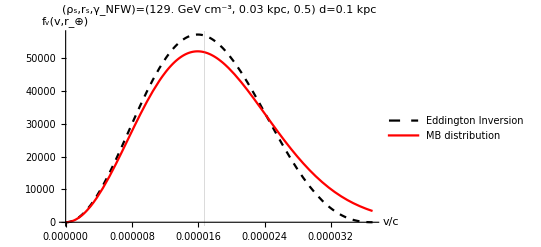

```mathematica
Plot[
{c fvNDInterp[β c],c PDF[MaxwellDistribution[σMB],β c]},
{β,vRef/c vNDMin,vRef/c vNDMax},
PlotStyle->{{Black,Dashed},Red},
PlotLegends->{"Eddington Inversion","MB distribution"},
AxesLabel->{Style["v/c",16], Style["f_v(v,r_⊕)",14]},
PlotLabel->Style["(ρ_s,r_s,γ_NFW)=("<>ToString[ρs/.paramSubs]<>" GeV cm^-3, "<>ToString[rs/.paramSubs]<>" kpc, "<>ToString[γnfw/.paramSubs]<>")\nd="<>ToString[d]<>" kpc",13],
GridLines->{{NIntegrate[v/c fvNDInterp[v],{v,0,vRef vNDMax}]},{}}
]
```

Means of the MB and EI distributions

```mathematica
Mean[MaxwellDistribution[σMB]]
```

4743.3

```mathematica
NIntegrate[v fvNDInterp[v],{v,0,vRef vNDMax}]
```

4418.6

## (Virial) mass of halo

The halo mass within a radius r is just
	M(r)=4π∫_0^r ⅆr r^2 ρ(r).
While this is finite for the TT halo, lim_(r→∞) M(r) is divergent for profiles like the NFW. A common prescription is to instead take the halo boundary to be the virial radius, which is defined by
	ρ(r_vir)=ρ_c,
where ρ_c is the critical density. Another common parameter when discussing NFW profiles is the concentration c:
	c=r_vir/r_s.
Generally r_vir must be determined numerically. Below I provide analytic forms for M(r).

### NFW

```mathematica
massNFW[r_]=Integrate[4π rp^2 ρnfw[rp],rp]/.rp->r//FullSimplify
```

4 π ρs rs^3 (rs/r)^γnfw ((r rs^-γnfw (r+rs)^(γnfw-2) (2 γnfw r-3 r+γnfw rs-2 rs))/(γnfw^2-3 γnfw+2)-(-r/rs)^γnfw -r/rs1-γnfwγnfw)

```mathematica
FullSimplify[Beta[-r/rs,1-γ,γ],Assumptions->{3/2>γ>0,r>0,rs>0}]
```

-r/rs1-γγ

```mathematica
?Beta
```

Beta[a,b] gives the Euler beta function Β(a,b). 
Beta[z,a,b] gives the incomplete beta function Β_z(a,b).

```mathematica
ⅈ Beta[-x,1-γ,γ]//FullSimplify[#,Assumptions->{1>γ>0,x>1}]&
```

ⅈ -x1-γγ

### TT

```mathematica
massTT[r_]=Integrate[4π rp^2 ρtt[rp],{rp,0,∞}]/.rp->r//FullSimplify
```

4 π ρ0 Rb^3 3-γtt

```mathematica
4π
```

## Different possible cuts for n-body probabilities

These cuts are all relative to the benchmark values I derived in my contour plots.

```mathematica
ρsBM=0.5;
rsBM=0.5;
LBM=Lnfw/.{ρs->ρsBM,rs->rsBM,γnfw->0.5};
```

### Ben's original cut

This is meant to integrate over halos that are at least as point-like as the benchmark one. However, this is extremely sensitive to the smallest subhalo mass resolvable in the simulation being used, since requiring r_s to be smaller than the benchmark value corresponds to a less massive subhalo, and Pr(M) grows dramatically for smaller halo masses.

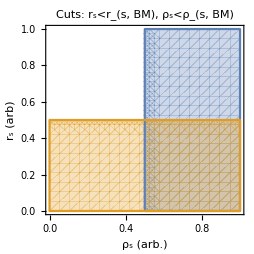

```mathematica
RegionPlot[
{ρs>ρsBM,rs<rsBM},{ρs,0,2ρsBM},{rs,0,2rsBM},
PlotRange->{{0,2ρsBM},{0,2rsBM}},
FrameLabel->{"ρ_s (arb.)", "r_s (arb)"},
PlotLabel->"Cuts: r_s<r_(s, BM), ρ_s<ρ_(s, BM)"
]
```

### Ben's next idea

```mathematica
Evaluate[Lnfw/.γnfw->0.5]>LBM
```

1.0472 ρs^2 rs^3>0.0327249

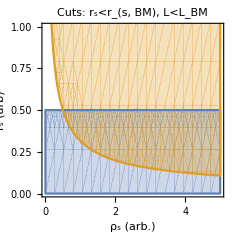

```mathematica
RegionPlot[
{rs<rsBM,Evaluate[Lnfw/.γnfw->0.5]>LBM },
{ρs,0,10ρsBM},
{rs,0,10rsBM},
PlotRange->{{0,10ρsBM},{0,2rsBM}},FrameLabel->{"ρ_s (arb.)", "r_s (arb)"},
PlotLabel->"Cuts: r_s<r_(s, BM), L<L_BM"
]
```

# Old stuff

#### Dimensional

```mathematica
fv[v_,r_,ρ_,dρ dr_,d2ρ dr2_,ψ_,dψ dr_,d2ψ dr2_,params_]:=Module[{fact,integrand,int,vu,ρu,dρ dru,d2ρ dr2u,ψu,dψ dru,d2ψ dr2u,rBound},
(* Convert to SI units *)
vu=v;
ρu[rp_]:=(10^2)^3 GeV to kg ρ[rp];
dρ dru[rp_]:=(10^2)^3(GeV to kg)/(kpc to m)dρ dr[rp];
d2ρ dr2u[rp_]:=(10^2)^3(GeV to kg)/(kpc to m)^2 d2ρ dr2[rp];
ψu[rp_]:=(10^2 kpc to m)^3(GeV to kg)/(kpc to m)ψ[rp];
dψ dru[rp_]:=(10^2 kpc to m)^3(GeV to kg)/(kpc to m)^2 dψ dr[rp];
d2ψ dr2u[rp_]:=(10^2 kpc to m)^3(GeV to kg)/(kpc to m)^3 d2ψ dr2[rp];

(* Normalization *)
fact=(4π vu^2)/ρu[r] /.params;
(* Determine integration bound *)
rBound=rp/.FindRoot[Re[ψu[r]-1/2 vu^2-ψu[rp]/.params/.GSub]==0,{rp,r}];
integrand[rp_]=1/(√(ψu[r]-1/2 vu^2-ψu[rp]))1/(dψ dru[rp])(d2ρ dr2u[rp]-1/(dψ dru[rp])d2ψ dr2u[rp]dρ dru[rp])//Simplify;
int=NIntegrate[Re[integrand[rp]/.params/.GSub],{rp,∞,rBound}];

fact*int
]
```

#### Compute speed distribution (dimensional)

```mathematica
(* Choose some clump parameters *)
paramSubs={ρs->0.184,rs->24.42,γnfw->0.99}; (* MW halo *)
d=8.;

paramSubs={ρs->10.,rs->0.1,γnfw->0.5};
d=1.;

(*paramSubs={ρs->100.,rs->3 10^-2,γnfw->0.5};d=0.1;*)
```

```mathematica
(* Find DM escape velocity *)
vMax=Re[vEsc/.FindRoot[(10^2 kpc to m)^3(GeV to kg)/(kpc to m)ψnfw[d]-1/2 vEsc^2==0/.paramSubs/.GSub,{vEsc,544 10^3}]];
vMin=0;

(* Compute Subscript[f, v](v,r) over a grid *)
fvs=Table[{v,fv[v,d,ρnfw,dρ drnfw,d2ρ dr2nfw,ψnfw,dψ drnfw,d2ψ dr2nfw,paramSubs]},{v,vMin,vMax,vMax/100}];

(* Construct an interpolator *)
fvInterp=Interpolation[fvs];

(* Find "equivalent" Maxwell-Boltzmann distribution *)
σMB=(v/.Maximize[{fvInterp[v],vMin<v<vMax},v]⟦2⟧)/(√2);
```

Plot speed distribution

```mathematica
Plot[
{7.5 10^-19*PDF[MaxwellDistribution[σMB],c voverc],fvInterp[c voverc]},{voverc,vMin/c,vMax/c},
PlotStyle->{{Black,Dashed},Red},
PlotLegends->{"Maxwell-Boltzmann","f_v(v,r)"},
AxesLabel->{"v/c", "PDF"}
]
```